```mathematica
strat=RulesTree[1->{2->{4,6},3->{5,4}}]
```

-Graphics-

```mathematica
compList=Subsets[{1,2,3,4},{2}]
```

{{1,2},{1,3},{1,4},{2,3},{2,4},{3,4}}

```mathematica
filter[i_,b_,L_List]:=L/.(l_List:>Nothing[]/;Equivalent[l[[First[compList[[i]]]]]>=l[[Last[compList[[i]]]]],b])
```

```mathematica
filter[3,False,Permutations[{1,2,3,4}]]
```

{{2,3,4,1},{2,4,3,1},{3,1,4,2},{3,2,4,1},{3,4,1,2},{3,4,2,1},{4,1,2,3},{4,1,3,2},{4,2,1,3},{4,2,3,1},{4,3,1,2},{4,3,2,1}}

```mathematica
filter[3,True,Permutations[{1,2,3,4}]]
```

{{1,2,3,4},{1,2,4,3},{1,3,2,4},{1,3,4,2},{1,4,2,3},{1,4,3,2},{2,1,3,4},{2,1,4,3},{2,3,1,4},{2,4,1,3},{3,1,2,4},{3,2,1,4}}

```mathematica
permL=Permutations[{1,2,3,4}]
```

{{1,2,3,4},{1,2,4,3},{1,3,2,4},{1,3,4,2},{1,4,2,3},{1,4,3,2},{2,1,3,4},{2,1,4,3},{2,3,1,4},{2,3,4,1},{2,4,1,3},{2,4,3,1},{3,1,2,4},{3,1,4,2},{3,2,1,4},{3,2,4,1},{3,4,1,2},{3,4,2,1},{4,1,2,3},{4,1,3,2},{4,2,1,3},{4,2,3,1},{4,3,1,2},{4,3,2,1}}

```mathematica
filter[2,True,filter[1,True,permL]]
```

{{1,2,3,4},{1,2,4,3},{1,3,2,4},{1,3,4,2},{1,4,2,3},{1,4,3,2},{2,3,4,1},{2,4,3,1}}

```mathematica
TreePosition[strat,_,{-1}]
```

{{1,1},{1,2},{2,1},{2,2}}

```mathematica
TreeExtract[strat,{1,1},TreeData]
```

4

```mathematica
TreePosition[strat,_,{-1}]
```

{{1,1},{1,2},{2,1},{2,2}}

```mathematica
filterL[l_]:=Module[
{reducedL},
reducedL=permL;
For[i=1,i<=Length[l],i++,
reducedL=filter[TreeExtract[strat,l[[;;i-1]]/.{}->Sequence[],TreeData],l[[i]]/.{1->True,2->False},reducedL];
];

reducedL
]
```

```mathematica
filterL[{1,2}]
```

{{2,3,1,4},{2,4,1,3},{3,4,1,2},{3,4,2,1}}

```mathematica
TreeExtract[strat,TreeData]
```

1

```mathematica
filterLT[l_,strat_]:=Module[
{reducedL},
reducedL=permL;
For[i=1,i<=Length[l],i++,
reducedL=filter[TreeExtract[strat,l[[;;i-1]]/.{}->Sequence[],TreeData],l[[i]]/.{1->True,2->False},reducedL];
];
reducedL
]
```

```mathematica
LeafFilters[strat_]:=Quiet[filterLT[#,strat]&/@TreePosition[strat,_,{-1}]]
```

```mathematica
strat=RulesTree[1->{2->{5->{6->{1,1},6->{1,1}},6->{1,1}},3->{5,4}}]
Length/@LeafFilters[strat]
```

-Graphics-

{2,1,1,4,3,1,4,8}

```mathematica
filterLT[{1,1,1,1},strat]
```

Part::partw: Part 4 of {{1,2,3,4},{1,2,4,3},{1,3,2,4}} does not exist.

{{1,2,3,4},{1,3,2,4}}

```mathematica
Length[compList]
```

6

```mathematica
(Length/@LeafFilters[#])&/@Table[RulesTree[i1->{"",""}],{i1,6}]
```

{{12,12},{12,12},{12,12},{12,12},{12,12},{12,12}}

```mathematica
(Length/@LeafFilters[#])&/@Flatten[Table[RulesTree[i1->{i2->{"",""},""}],{i1,6},{i2,6}]]
```

{{12,0,12},{8,4,12},{8,4,12},{4,8,12},{4,8,12},{6,6,12},{8,4,12},{12,0,12},{8,4,12},{8,4,12},{6,6,12},{4,8,12},{8,4,12},{8,4,12},{12,0,12},{6,6,12},{8,4,12},{8,4,12},{4,8,12},{8,4,12},{6,6,12},{12,0,12},{8,4,12},{4,8,12},{4,8,12},{6,6,12},{8,4,12},{8,4,12},{12,0,12},{8,4,12},{6,6,12},{4,8,12},{8,4,12},{4,8,12},{8,4,12},{12,0,12}}

```mathematica
(Length/@LeafFilters[#])&/@Flatten[Table[RulesTree[i1->{i2->{"",""},i3->{"",""}}],{i1,6},{i2,6},{i3,6}]]
```

{{12,0,0,12},{12,0,4,8},{12,0,4,8},{12,0,8,4},{12,0,8,4},{12,0,6,6},{8,4,0,12},{8,4,4,8},{8,4,4,8},{8,4,8,4},{8,4,8,4},{8,4,6,6},{8,4,0,12},{8,4,4,8},{8,4,4,8},{8,4,8,4},{8,4,8,4},{8,4,6,6},{4,8,0,12},{4,8,4,8},{4,8,4,8},{4,8,8,4},{4,8,8,4},{4,8,6,6},{4,8,0,12},{4,8,4,8},{4,8,4,8},{4,8,8,4},{4,8,8,4},{4,8,6,6},{6,6,0,12},{6,6,4,8},{6,6,4,8},{6,6,8,4},{6,6,8,4},{6,6,6,6},{8,4,4,8},{8,4,0,12},{8,4,4,8},{8,4,4,8},{8,4,6,6},{8,4,8,4},{12,0,4,8},{12,0,0,12},{12,0,4,8},{12,0,4,8},{12,0,6,6},{12,0,8,4},{8,4,4,8},{8,4,0,12},{8,4,4,8},{8,4,4,8},{8,4,6,6},{8,4,8,4},{8,4,4,8},{8,4,0,12},{8,4,4,8},{8,4,4,8},{8,4,6,6},{8,4,8,4},{6,6,4,8},{6,6,0,12},{6,6,4,8},{6,6,4,8},{6,6,6,6},{6,6,8,4},{4,8,4,8},{4,8,0,12},{4,8,4,8},{4,8,4,8},{4,8,6,6},{4,8,8,4},{8,4,4,8},{8,4,4,8},{8,4,0,12},{8,4,6,6},{8,4,4,8},{8,4,4,8},{8,4,4,8},{8,4,4,8},{8,4,0,12},{8,4,6,6},{8,4,4,8},{8,4,4,8},{12,0,4,8},{12,0,4,8},{12,0,0,12},{12,0,6,6},{12,0,4,8},{12,0,4,8},{6,6,4,8},{6,6,4,8},{6,6,0,12},{6,6,6,6},{6,6,4,8},{6,6,4,8},{8,4,4,8},{8,4,4,8},{8,4,0,12},{8,4,6,6},{8,4,4,8},{8,4,4,8},{8,4,4,8},{8,4,4,8},{8,4,0,12},{8,4,6,6},{8,4,4,8},{8,4,4,8},{4,8,8,4},{4,8,4,8},{4,8,6,6},{4,8,0,12},{4,8,4,8},{4,8,8,4},{8,4,8,4},{8,4,4,8},{8,4,6,6},{8,4,0,12},{8,4,4,8},{8,4,8,4},{6,6,8,4},{6,6,4,8},{6,6,6,6},{6,6,0,12},{6,6,4,8},{6,6,8,4},{12,0,8,4},{12,0,4,8},{12,0,6,6},{12,0,0,12},{12,0,4,8},{12,0,8,4},{8,4,8,4},{8,4,4,8},{8,4,6,6},{8,4,0,12},{8,4,4,8},{8,4,8,4},{4,8,8,4},{4,8,4,8},{4,8,6,6},{4,8,0,12},{4,8,4,8},{4,8,8,4},{4,8,8,4},{4,8,6,6},{4,8,4,8},{4,8,4,8},{4,8,0,12},{4,8,4,8},{6,6,8,4},{6,6,6,6},{6,6,4,8},{6,6,4,8},{6,6,0,12},{6,6,4,8},{8,4,8,4},{8,4,6,6},{8,4,4,8},{8,4,4,8},{8,4,0,12},{8,4,4,8},{8,4,8,4},{8,4,6,6},{8,4,4,8},{8,4,4,8},{8,4,0,12},{8,4,4,8},{12,0,8,4},{12,0,6,6},{12,0,4,8},{12,0,4,8},{12,0,0,12},{12,0,4,8},{8,4,8,4},{8,4,6,6},{8,4,4,8},{8,4,4,8},{8,4,0,12},{8,4,4,8},{6,6,6,6},{6,6,8,4},{6,6,4,8},{6,6,8,4},{6,6,4,8},{6,6,0,12},{4,8,6,6},{4,8,8,4},{4,8,4,8},{4,8,8,4},{4,8,4,8},{4,8,0,12},{8,4,6,6},{8,4,8,4},{8,4,4,8},{8,4,8,4},{8,4,4,8},{8,4,0,12},{4,8,6,6},{4,8,8,4},{4,8,4,8},{4,8,8,4},{4,8,4,8},{4,8,0,12},{8,4,6,6},{8,4,8,4},{8,4,4,8},{8,4,8,4},{8,4,4,8},{8,4,0,12},{12,0,6,6},{12,0,8,4},{12,0,4,8},{12,0,8,4},{12,0,4,8},{12,0,0,12}}

```mathematica
(Length/@LeafFilters[#])&/@Flatten[Table[RulesTree[i1->{i2->{i4->{"",""},""},i3->{"",""}}],{i1,6},{i2,Delete[Range[6],i1]},{i3,Delete[Range[6],i1]},{i4,Delete[Range[6],{{i1},{i2}}]}]]
```

{{6,2,4,4,8},{4,4,4,4,8},{3,5,4,4,8},{3,5,4,4,8},{6,2,4,4,8},{4,4,4,4,8},{3,5,4,4,8},{3,5,4,4,8},{6,2,4,8,4},{4,4,4,8,4},{3,5,4,8,4},{3,5,4,8,4},{6,2,4,8,4},{4,4,4,8,4},{3,5,4,8,4},{3,5,4,8,4},{6,2,4,6,6},{4,4,4,6,6},{3,5,4,6,6},{3,5,4,6,6},{6,2,4,4,8},{3,5,4,4,8},{4,4,4,4,8},{5,3,4,4,8},{6,2,4,4,8},{3,5,4,4,8},{4,4,4,4,8},{5,3,4,4,8},{6,2,4,8,4},{3,5,4,8,4},{4,4,4,8,4},{5,3,4,8,4},{6,2,4,8,4},{3,5,4,8,4},{4,4,4,8,4},{5,3,4,8,4},{6,2,4,6,6},{3,5,4,6,6},{4,4,4,6,6},{5,3,4,6,6},{4,0,8,4,8},{3,1,8,4,8},{2,2,8,4,8},{1,3,8,4,8},{4,0,8,4,8},{3,1,8,4,8},{2,2,8,4,8},{1,3,8,4,8},{4,0,8,8,4},{3,1,8,8,4},{2,2,8,8,4},{1,3,8,8,4},{4,0,8,8,4},{3,1,8,8,4},{2,2,8,8,4},{1,3,8,8,4},{4,0,8,6,6},{3,1,8,6,6},{2,2,8,6,6},{1,3,8,6,6},{3,1,8,4,8},{4,0,8,4,8},{2,2,8,4,8},{3,1,8,4,8},{3,1,8,4,8},{4,0,8,4,8},{2,2,8,4,8},{3,1,8,4,8},{3,1,8,8,4},{4,0,8,8,4},{2,2,8,8,4},{3,1,8,8,4},{3,1,8,8,4},{4,0,8,8,4},{2,2,8,8,4},{3,1,8,8,4},{3,1,8,6,6},{4,0,8,6,6},{2,2,8,6,6},{3,1,8,6,6},{3,3,6,4,8},{5,1,6,4,8},{1,5,6,4,8},{3,3,6,4,8},{3,3,6,4,8},{5,1,6,4,8},{1,5,6,4,8},{3,3,6,4,8},{3,3,6,8,4},{5,1,6,8,4},{1,5,6,8,4},{3,3,6,8,4},{3,3,6,8,4},{5,1,6,8,4},{1,5,6,8,4},{3,3,6,8,4},{3,3,6,6,6},{5,1,6,6,6},{1,5,6,6,6},{3,3,6,6,6},{6,2,4,4,8},{4,4,4,4,8},{3,5,4,4,8},{3,5,4,4,8},{6,2,4,4,8},{4,4,4,4,8},{3,5,4,4,8},{3,5,4,4,8},{6,2,4,4,8},{4,4,4,4,8},{3,5,4,4,8},{3,5,4,4,8},{6,2,4,6,6},{4,4,4,6,6},{3,5,4,6,6},{3,5,4,6,6},{6,2,4,8,4},{4,4,4,8,4},{3,5,4,8,4},{3,5,4,8,4},{6,2,4,4,8},{5,3,4,4,8},{5,3,4,4,8},{4,4,4,4,8},{6,2,4,4,8},{5,3,4,4,8},{5,3,4,4,8},{4,4,4,4,8},{6,2,4,4,8},{5,3,4,4,8},{5,3,4,4,8},{4,4,4,4,8},{6,2,4,6,6},{5,3,4,6,6},{5,3,4,6,6},{4,4,4,6,6},{6,2,4,8,4},{5,3,4,8,4},{5,3,4,8,4},{4,4,4,8,4},{4,4,4,4,8},{5,3,4,4,8},{5,3,4,4,8},{2,6,4,4,8},{4,4,4,4,8},{5,3,4,4,8},{5,3,4,4,8},{2,6,4,4,8},{4,4,4,4,8},{5,3,4,4,8},{5,3,4,4,8},{2,6,4,4,8},{4,4,4,6,6},{5,3,4,6,6},{5,3,4,6,6},{2,6,4,6,6},{4,4,4,8,4},{5,3,4,8,4},{5,3,4,8,4},{2,6,4,8,4},{3,3,6,4,8},{5,1,6,4,8},{5,1,6,4,8},{3,3,6,4,8},{3,3,6,4,8},{5,1,6,4,8},{5,1,6,4,8},{3,3,6,4,8},{3,3,6,4,8},{5,1,6,4,8},{5,1,6,4,8},{3,3,6,4,8},{3,3,6,6,6},{5,1,6,6,6},{5,1,6,6,6},{3,3,6,6,6},{3,3,6,8,4},{5,1,6,8,4},{5,1,6,8,4},{3,3,6,8,4},{3,1,8,4,8},{4,0,8,4,8},{2,2,8,4,8},{3,1,8,4,8},{3,1,8,4,8},{4,0,8,4,8},{2,2,8,4,8},{3,1,8,4,8},{3,1,8,4,8},{4,0,8,4,8},{2,2,8,4,8},{3,1,8,4,8},{3,1,8,6,6},{4,0,8,6,6},{2,2,8,6,6},{3,1,8,6,6},{3,1,8,8,4},{4,0,8,8,4},{2,2,8,8,4},{3,1,8,8,4},{6,2,4,4,8},{3,5,4,4,8},{4,4,4,4,8},{5,3,4,4,8},{6,2,4,4,8},{3,5,4,4,8},{4,4,4,4,8},{5,3,4,4,8},{6,2,4,6,6},{3,5,4,6,6},{4,4,4,6,6},{5,3,4,6,6},{6,2,4,4,8},{3,5,4,4,8},{4,4,4,4,8},{5,3,4,4,8},{6,2,4,4,8},{3,5,4,4,8},{4,4,4,4,8},{5,3,4,4,8},{6,2,4,4,8},{5,3,4,4,8},{5,3,4,4,8},{4,4,4,4,8},{6,2,4,4,8},{5,3,4,4,8},{5,3,4,4,8},{4,4,4,4,8},{6,2,4,6,6},{5,3,4,6,6},{5,3,4,6,6},{4,4,4,6,6},{6,2,4,4,8},{5,3,4,4,8},{5,3,4,4,8},{4,4,4,4,8},{6,2,4,4,8},{5,3,4,4,8},{5,3,4,4,8},{4,4,4,4,8},{3,3,6,4,8},{5,1,6,4,8},{5,1,6,4,8},{3,3,6,4,8},{3,3,6,4,8},{5,1,6,4,8},{5,1,6,4,8},{3,3,6,4,8},{3,3,6,6,6},{5,1,6,6,6},{5,1,6,6,6},{3,3,6,6,6},{3,3,6,4,8},{5,1,6,4,8},{5,1,6,4,8},{3,3,6,4,8},{3,3,6,4,8},{5,1,6,4,8},{5,1,6,4,8},{3,3,6,4,8},{4,4,4,4,8},{5,3,4,4,8},{5,3,4,4,8},{6,2,4,4,8},{4,4,4,4,8},{5,3,4,4,8},{5,3,4,4,8},{6,2,4,4,8},{4,4,4,6,6},{5,3,4,6,6},{5,3,4,6,6},{6,2,4,6,6},{4,4,4,4,8},{5,3,4,4,8},{5,3,4,4,8},{6,2,4,4,8},{4,4,4,4,8},{5,3,4,4,8},{5,3,4,4,8},{6,2,4,4,8},{5,3,4,4,8},{4,4,4,4,8},{3,5,4,4,8},{6,2,4,4,8},{5,3,4,4,8},{4,4,4,4,8},{3,5,4,4,8},{6,2,4,4,8},{5,3,4,6,6},{4,4,4,6,6},{3,5,4,6,6},{6,2,4,6,6},{5,3,4,4,8},{4,4,4,4,8},{3,5,4,4,8},{6,2,4,4,8},{5,3,4,4,8},{4,4,4,4,8},{3,5,4,4,8},{6,2,4,4,8},{4,0,8,8,4},{3,1,8,8,4},{2,2,8,8,4},{1,3,8,8,4},{4,0,8,4,8},{3,1,8,4,8},{2,2,8,4,8},{1,3,8,4,8},{4,0,8,6,6},{3,1,8,6,6},{2,2,8,6,6},{1,3,8,6,6},{4,0,8,4,8},{3,1,8,4,8},{2,2,8,4,8},{1,3,8,4,8},{4,0,8,8,4},{3,1,8,8,4},{2,2,8,8,4},{1,3,8,8,4},{4,4,4,8,4},{5,3,4,8,4},{5,3,4,8,4},{2,6,4,8,4},{4,4,4,4,8},{5,3,4,4,8},{5,3,4,4,8},{2,6,4,4,8},{4,4,4,6,6},{5,3,4,6,6},{5,3,4,6,6},{2,6,4,6,6},{4,4,4,4,8},{5,3,4,4,8},{5,3,4,4,8},{2,6,4,4,8},{4,4,4,8,4},{5,3,4,8,4},{5,3,4,8,4},{2,6,4,8,4},{3,3,6,8,4},{5,1,6,8,4},{5,1,6,8,4},{3,3,6,8,4},{3,3,6,4,8},{5,1,6,4,8},{5,1,6,4,8},{3,3,6,4,8},{3,3,6,6,6},{5,1,6,6,6},{5,1,6,6,6},{3,3,6,6,6},{3,3,6,4,8},{5,1,6,4,8},{5,1,6,4,8},{3,3,6,4,8},{3,3,6,8,4},{5,1,6,8,4},{5,1,6,8,4},{3,3,6,8,4},{2,6,4,8,4},{5,3,4,8,4},{5,3,4,8,4},{4,4,4,8,4},{2,6,4,4,8},{5,3,4,4,8},{5,3,4,4,8},{4,4,4,4,8},{2,6,4,6,6},{5,3,4,6,6},{5,3,4,6,6},{4,4,4,6,6},{2,6,4,4,8},{5,3,4,4,8},{5,3,4,4,8},{4,4,4,4,8},{2,6,4,8,4},{5,3,4,8,4},{5,3,4,8,4},{4,4,4,8,4},{1,3,8,8,4},{2,2,8,8,4},{3,1,8,8,4},{4,0,8,8,4},{1,3,8,4,8},{2,2,8,4,8},{3,1,8,4,8},{4,0,8,4,8},{1,3,8,6,6},{2,2,8,6,6},{3,1,8,6,6},{4,0,8,6,6},{1,3,8,4,8},{2,2,8,4,8},{3,1,8,4,8},{4,0,8,4,8},{1,3,8,8,4},{2,2,8,8,4},{3,1,8,8,4},{4,0,8,8,4},{3,1,8,8,4},{4,0,8,8,4},{2,2,8,8,4},{3,1,8,8,4},{3,1,8,6,6},{4,0,8,6,6},{2,2,8,6,6},{3,1,8,6,6},{3,1,8,4,8},{4,0,8,4,8},{2,2,8,4,8},{3,1,8,4,8},{3,1,8,4,8},{4,0,8,4,8},{2,2,8,4,8},{3,1,8,4,8},{3,1,8,4,8},{4,0,8,4,8},{2,2,8,4,8},{3,1,8,4,8},{3,3,6,8,4},{5,1,6,8,4},{5,1,6,8,4},{3,3,6,8,4},{3,3,6,6,6},{5,1,6,6,6},{5,1,6,6,6},{3,3,6,6,6},{3,3,6,4,8},{5,1,6,4,8},{5,1,6,4,8},{3,3,6,4,8},{3,3,6,4,8},{5,1,6,4,8},{5,1,6,4,8},{3,3,6,4,8},{3,3,6,4,8},{5,1,6,4,8},{5,1,6,4,8},{3,3,6,4,8},{4,4,4,8,4},{5,3,4,8,4},{5,3,4,8,4},{6,2,4,8,4},{4,4,4,6,6},{5,3,4,6,6},{5,3,4,6,6},{6,2,4,6,6},{4,4,4,4,8},{5,3,4,4,8},{5,3,4,4,8},{6,2,4,4,8},{4,4,4,4,8},{5,3,4,4,8},{5,3,4,4,8},{6,2,4,4,8},{4,4,4,4,8},{5,3,4,4,8},{5,3,4,4,8},{6,2,4,4,8},{2,6,4,8,4},{5,3,4,8,4},{5,3,4,8,4},{4,4,4,8,4},{2,6,4,6,6},{5,3,4,6,6},{5,3,4,6,6},{4,4,4,6,6},{2,6,4,4,8},{5,3,4,4,8},{5,3,4,4,8},{4,4,4,4,8},{2,6,4,4,8},{5,3,4,4,8},{5,3,4,4,8},{4,4,4,4,8},{2,6,4,4,8},{5,3,4,4,8},{5,3,4,4,8},{4,4,4,4,8},{3,5,4,8,4},{3,5,4,8,4},{6,2,4,8,4},{4,4,4,8,4},{3,5,4,6,6},{3,5,4,6,6},{6,2,4,6,6},{4,4,4,6,6},{3,5,4,4,8},{3,5,4,4,8},{6,2,4,4,8},{4,4,4,4,8},{3,5,4,4,8},{3,5,4,4,8},{6,2,4,4,8},{4,4,4,4,8},{3,5,4,4,8},{3,5,4,4,8},{6,2,4,4,8},{4,4,4,4,8},{3,3,6,6,6},{5,1,6,6,6},{1,5,6,6,6},{3,3,6,6,6},{3,3,6,8,4},{5,1,6,8,4},{1,5,6,8,4},{3,3,6,8,4},{3,3,6,4,8},{5,1,6,4,8},{1,5,6,4,8},{3,3,6,4,8},{3,3,6,8,4},{5,1,6,8,4},{1,5,6,8,4},{3,3,6,8,4},{3,3,6,4,8},{5,1,6,4,8},{1,5,6,4,8},{3,3,6,4,8},{3,1,8,6,6},{4,0,8,6,6},{2,2,8,6,6},{3,1,8,6,6},{3,1,8,8,4},{4,0,8,8,4},{2,2,8,8,4},{3,1,8,8,4},{3,1,8,4,8},{4,0,8,4,8},{2,2,8,4,8},{3,1,8,4,8},{3,1,8,8,4},{4,0,8,8,4},{2,2,8,8,4},{3,1,8,8,4},{3,1,8,4,8},{4,0,8,4,8},{2,2,8,4,8},{3,1,8,4,8},{5,3,4,6,6},{4,4,4,6,6},{3,5,4,6,6},{6,2,4,6,6},{5,3,4,8,4},{4,4,4,8,4},{3,5,4,8,4},{6,2,4,8,4},{5,3,4,4,8},{4,4,4,4,8},{3,5,4,4,8},{6,2,4,4,8},{5,3,4,8,4},{4,4,4,8,4},{3,5,4,8,4},{6,2,4,8,4},{5,3,4,4,8},{4,4,4,4,8},{3,5,4,4,8},{6,2,4,4,8},{1,3,8,6,6},{2,2,8,6,6},{3,1,8,6,6},{4,0,8,6,6},{1,3,8,8,4},{2,2,8,8,4},{3,1,8,8,4},{4,0,8,8,4},{1,3,8,4,8},{2,2,8,4,8},{3,1,8,4,8},{4,0,8,4,8},{1,3,8,8,4},{2,2,8,8,4},{3,1,8,8,4},{4,0,8,8,4},{1,3,8,4,8},{2,2,8,4,8},{3,1,8,4,8},{4,0,8,4,8},{3,5,4,6,6},{3,5,4,6,6},{6,2,4,6,6},{4,4,4,6,6},{3,5,4,8,4},{3,5,4,8,4},{6,2,4,8,4},{4,4,4,8,4},{3,5,4,4,8},{3,5,4,4,8},{6,2,4,4,8},{4,4,4,4,8},{3,5,4,8,4},{3,5,4,8,4},{6,2,4,8,4},{4,4,4,8,4},{3,5,4,4,8},{3,5,4,4,8},{6,2,4,4,8},{4,4,4,4,8}}

```mathematica
Log[2,4!]//N
```

4.58496

```mathematica
Flatten[Table[RulesTree[i1->{i2->{i4->{i5->{"",""},""},""},i3->{"",""}}],{i1,6},{i2,Delete[Range[6],i1]},{i3,Delete[Range[6],i1]},{i4,Delete[Range[6],{{i1},{i2}}]},{i5,Delete[Range[6],{{i1},{i2},{i4}}]}]]//First
```

-Graphics-

```mathematica
4!
```

24

```mathematica
l=RandomVariate[NormalDistribution[],10000000];
RepeatedTiming[MinMax[l]]
```

{0.00178012,{-5.27006,5.40554}}

```mathematica
l=RandomVariate[NormalDistribution[],100000000];
RepeatedTiming[MinMax[l]]
RepeatedTiming[Max[l]]
```

{0.0179642,{-5.43664,5.54341}}

{0.0146433,5.54341}

```mathematica
0.01905921875/0.001780123046875/10
```

1.07067

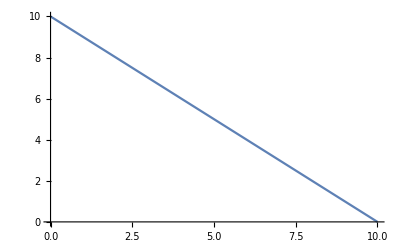

```mathematica
Plot[10-i,{i,0,10}]
```

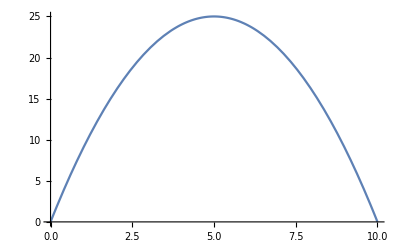

```mathematica
Plot[(10-i) i,{i,0,10}]
```

```mathematica
∫_0^ii (10-x)ⅆx
```

10 ii-ii^2/2

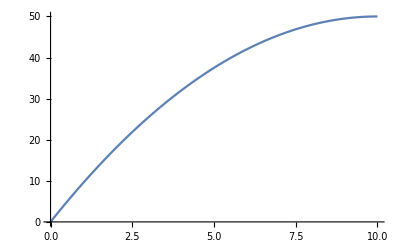

```mathematica
Plot[10 ii-ii^2/2,{ii,0,10}]
```

```mathematica
17.5/411 100
```

4.25791